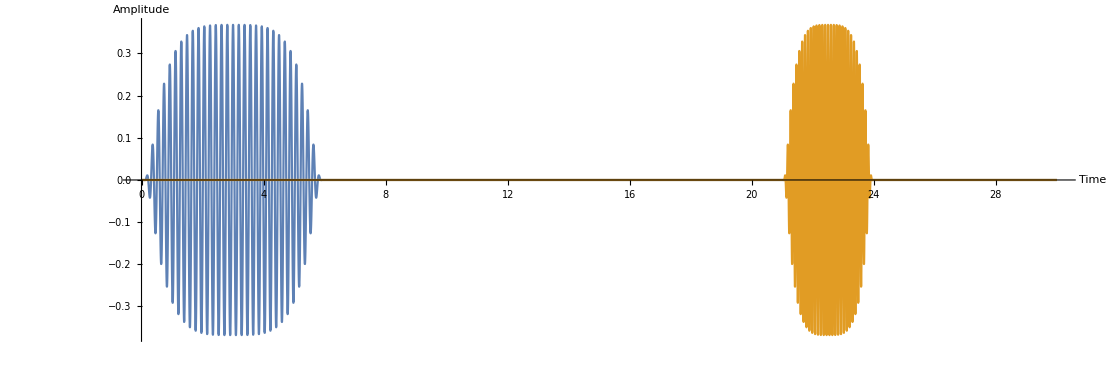

```mathematica
v1 =1;
s1 = 1/3;
w1[x_] = Piecewise[{{Exp[-1/(1-Abs[(s1 x-v1)^4])] Cos[100 (s1 x-v1)],-1+v1< s1 x < 1+v1}}];
v2 =15;
s2 = 2/3;
w2[x_] = Piecewise[{{Exp[-1/(1-Abs[(s2 x-v2)^4])] Cos[100 (s2 x-v2)],-1+v2< s2 x < 1+v2}}];
w[x_] = w1[x] + w2[x];
Plot[{w1[x], w2[x]}, {x, 0, 30}, PlotPoints->100,MaxRecursion->10,AxesLabel->{HoldForm[Time],HoldForm[Amplitude]},PlotLabel->None,LabelStyle->{20,GrayLevel[0]},TicksStyle->Directive[FontOpacity->0,FontSize->0], AspectRatio->1/3, AxesStyle->Arrowheads[{0.0,0.02}]]
```

```mathematica
c = 300;
num = 2 ^14;
range = 100;
dt = range/num //N;
dw = 2Pi/(num dt) //N;
time = Table[(j-num/2)*dt, {j, 1, num}];
freq =  Table[(j-num/2)*dw, {j, 1, num}];
ftdata = Table[w[time[[j]]], {j, 1, num}];
nydata = RotateLeft[ftdata, num/2-1];
ewdata = Chop[RotateRight[Fourier[nydata], num/2- 1]];
iwdata = ewdata*Conjugate[ewdata];
```

General::munfl: Exp[-3072.38] is too small to represent as a normalized machine number; precision may be lost.

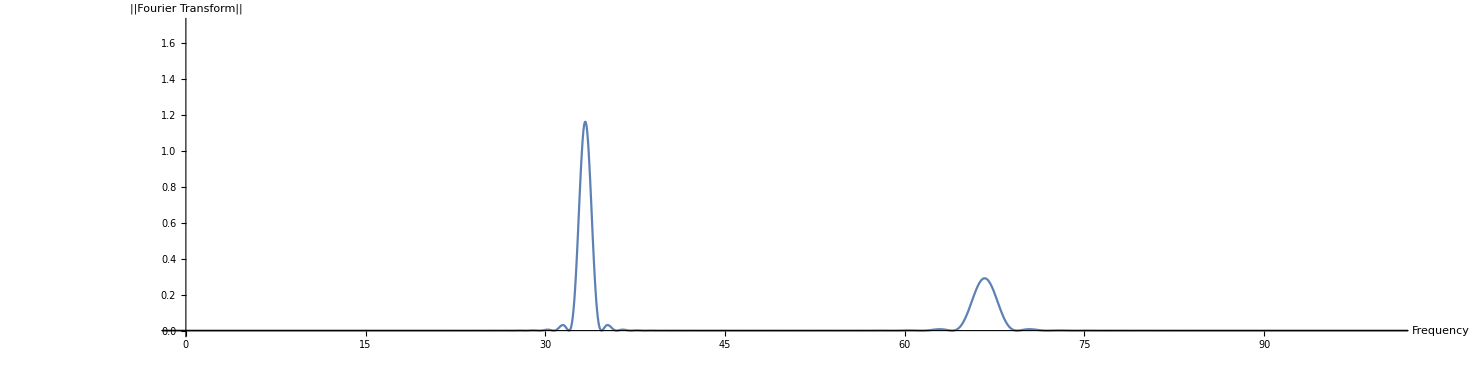

```mathematica
ListPlot[Table[{freq[[j]],iwdata[[j]]}, {j, 1, num}], PlotRange->{{0,100}, {0, 1.7}}, PlotJoined -> True, AspectRatio->1/4, AxesLabel->{HoldForm[Frequency],HoldForm["||Fourier Transform||"]},PlotLabel->None,LabelStyle->{20,GrayLevel[0]},TicksStyle->Directive[FontOpacity->0,FontSize->0], AxesStyle->Arrowheads[{0.0,0.02}]]
```